Vojtěch Myslivec, FIT ČVUT v Praze, 2015/2016

# Kryptosystém McEliece

Nutno vyhodnotit notebook src_mceliece.nb

## McEliece – Příklad použití

### Generování klíčů

```mathematica
m=4;
t=3;
{soukromyKlic,verejnyKlic,parametry}=generujMcEliece[m,t,True];
```

### Šifrováni

```mathematica
zprava=nahodnyPolynom[2,parametry⟦2⟧]
c=sifrujMcEliece[zprava,verejnyKlic,parametry]
```

### Dešifrováni

```mathematica
m=desifrujMcEliece[c,soukromyKlic,parametry]
m==zprava
```

## Časové složitosti

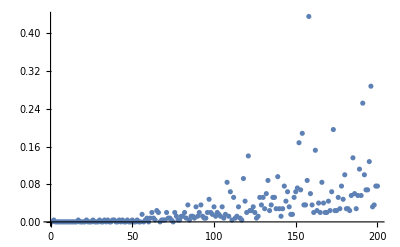

```mathematica
cas={#,Timing[nahodnaRegularniMatice[#]]⟦1⟧}&/@Range[200];
ListPlot[cas,PlotRange->All]
```